```mathematica
dim=8;
Clear[μ,η]
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
```

```mathematica
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}]
```

{B[0]→2 A[0]+Log[(η μ A[1]^2 A[3] A[5])/(√((η μ A[1]^2+A[5]) (η A[1]^2+μ A[5])) ((μ A[3]^2+η A[1]^2 A[5]) (A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]) (1+η μ A[1]^2 A[3]^2 A[5]))^(1/4))],B[1]→(A[1] A[2] √(μ A[3]^4+η A[1]^2 A[3]^2 A[5]+η μ^2 A[1]^2 A[3]^2 A[5]+η^2 μ A[1]^4 A[5]^2))/(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))^(1/4),B[2]→1/(√((η μ A[1]^2+A[5])/(η A[1]^2+μ A[5])) (((A[3]^2+η μ A[1]^2 A[5]) (1+η μ A[1]^2 A[3]^2 A[5]))/(μ^2 A[3]^2+η μ A[1]^2 (1+A[3]^4) A[5]+η^2 A[1]^4 A[3]^2 A[5]^2))^(1/4)),B[3]→A[3] A[4] √((η^2 μ A[1]^4+η A[1]^2 A[5]+η μ^2 A[1]^2 A[5]+μ A[5]^2)/(μ A[3]^2+η A[1]^2 A[5]+η μ^2 A[1]^2 A[3]^4 A[5]+η^2 μ A[1]^4 A[3]^2 A[5]^2)),B[4]→((A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/(√(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))),B[5]→((η μ A[1]^2+A[5]) (μ A[3]^2+η A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/((η A[1]^2+μ A[5]) √(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2)))}

```mathematica
Clear[μ,η]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
```

```mathematica
Clear[μ]
η=1;
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
μ=.001;
RGW;
RGW;
RGW;
(dA0dμ.Υ).(DLnZ1/.SAT)
```

60.

-2.

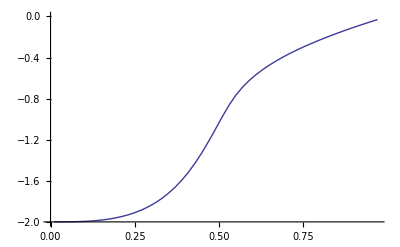

```mathematica
Clear[μ];
μmin=0.01;
μmax=1.0;
inc=0.02;
μVector=Range[μmin,μmax,inc];
InternalEnergy={};
k=500;
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
η=1;
Do[
InitRGW;
For[i=k,i>2,--i,
RGW;
];
AppendTo[InternalEnergy,-1.0/2^(k)*(dA0dμ.Υ).(DLnZ1/.SAT)],
{μ,μmin,μmax,inc}
];
Min[InternalEnergy]
ListLinePlot[Table[{Part[μVector,i],Part[InternalEnergy,i]},{i,1,IntegerPart[(μmax-μmin)/inc]}]]
```

```mathematica
InternalEnergy
```

{-2.,-1.99988,-1.99941,-1.99835,-1.99644,-1.99337,-1.98883,-1.9825,-1.97401,-1.96297,-1.94895,-1.93147,-1.91003,-1.88405,-1.85288,-1.81581,-1.77206,-1.72074,-1.66095,-1.59178,-1.5124,-1.42225,-1.32133,-1.21065,-1.093,-0.973854,-0.861769,-0.765664,-0.687222,-0.621866,-0.565753,-0.516398,-0.472157,-0.431898,-0.394817,-0.360323,-0.327972,-0.297423,-0.26841,-0.240719,-0.214179,-0.18865,-0.164016,-0.140179,-0.117058,-0.0945815,-0.0726912,-0.0513349,-0.0304677,-0.0100506}

{1.,0.0000216534}

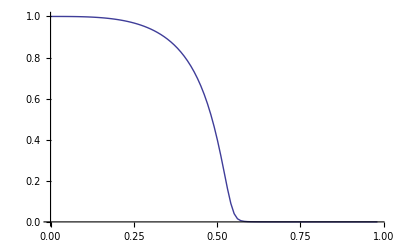

```mathematica
Clear[μ,η];
μmin=0.001;
μmax=1.0;
inc=0.01;
μVector=Range[μmin,μmax,inc];
Magnetization={};
k=64;
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.99999;
Do[
InitRGW;
For[i=k,i>2,--i,
RGW;
];
AppendTo[Magnetization,1.0/(2^(k+1)+1.0)*(dA0dη.Υ).(DLnZ1/.SAT)],
{μ,μmin,μmax,inc}
];
{Max[Magnetization],Min[Magnetization]}
ListLinePlot[Table[{Part[μVector,i],Part[Magnetization,i]},{i,1,IntegerPart[(μmax-μmin)/inc]}]]
```

```mathematica
Integer[1.1]
```

Integer[1.1]

```mathematica
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,5}];
```

```mathematica
k=4;
min=0.01;
max=1;
inc=0.1;
η=1;
μVector=Range[min,max,inc];
DLnZ1total={};
```

```mathematica
Do[InitRG;
For[i=k,i≥0,--i,
FullSimplify[RG,Assumptions->μ>0];
];
{AppendTo[DLnZ1total,DLnZ1/.SAT]},
{μ,min,max,inc}
];
Wtotal={};
Do[
InitRG;                                            (* initialize RG for each μ *)
Witer={};                                     (* reset the Witer list that will hold each W/.SAT value *)
AppendTo[Witer,W/.SAT];    (* first element in the Witer list when no RG has occured *)

For[i=k,i≥0,--i,
RG;
AppendTo[Witer,W/.SAT];  (* after RG, append W/.SAT to Witer. this is the equivalent of W^l in write-up *)
];
AppendTo[Wtotal,Witer],      (* the values stored in Witer are pushed to the Wtotal list *)
{μ,min,max,inc}                       (* Do loop goes from min to max in increments of inc *)
];
```

```mathematica
μindexMax=Ceiling[(max-min)/inc]
WindexMax=Part[Dimensions[Wtotal],2]
Υtotal={};
For[μindex=1,μindex≤μindexMax,++μindex,
(* Creates new list in which values of Υ will be stored *)
Υiter={};

(* Initially, Υ0 = W0 and is appended to the first element of Υtotal. *)
Υcurrent=Part[Part[Wtotal,μindex],1];
AppendTo[Υiter,Υcurrent];

(* This For loop calculates values of W^l.Υ^(l-1) and inserts them into the Υiter list. *)
For[Windex=2,Windex≤WindexMax,++Windex,
Υcurrent=(Part[Part[Wtotal,μindex],Windex]).Υcurrent;
AppendTo[Υiter,Υcurrent];
];

(* Υiter list for current μindex value is inserted into Υtotal list. *)
AppendTo[Υtotal,Υcurrent];
];
```

```mathematica
a=Array[KroneckerDelta,{3,3}]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
b={};
```

```mathematica
AppendTo[b,5*a]
```

{{{1,0,0},{0,1,0},{0,0,1}},{{2,0,0},{0,2,0},{0,0,2}},{{3,0,0},{0,3,0},{0,0,3}},{{4,0,0},{0,4,0},{0,0,4}},{{5,0,0},{0,5,0},{0,0,5}}}

```mathematica
Dimensions[b]
```

{5,3,3}

```mathematica
Part[b,2]
```

{{2,0,0},{0,2,0},{0,0,2}}

```mathematica
c={}
```

{}